```mathematica
directname="D:\\ProgramData\\mathmatica\\12.0\\AddOns\\Applications\\Radia\\";
SetDirectory[directname];
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
ct=0.05;  (*coil thickness in mm*)
cr=0.5; (*coil radius in mm*)
ww=0.05; (*wire width in mm*)
wt=0.05; (*wire thickness in mm*)
ic=5*^3; (*current in A*)
op=0.5;    (*coil open in mm*)
opa=ArcSin[op/2/cr];  (*half open angle*)
sl=0.55; (*length of straight part in mm*)
slf=0.2;(*length of the foot in mm*)
dd=0.7; (*distance between the disk in mm*)

c2={1,1,0};c1={0,1,1};thcn=0.001;

jc=ic/ct^2; (* Current Densities in A/mm^2 in coil*)
jw=ic/(wt*ww); (* Current Densities in A/mm^2 in wire*)
x1=-op/2;
x2=op/2;
x3=x4=x2;
y0=-cr*Cos[opa];
y1=y0-sl/2;
y2=y0-(sl-slf)/2;;
y3=y0-(sl-slf);
y4=y0-(sl-slf/2);
z1=z2=0;
z3=dd/2;
z4=dd;
wx1=wx2=wx3=wx4=ww;
wy1=sl;
wy2=sl-slf;
wy3=wt;
wy4=slf;
wz1=wz2=wz4=wt;
wz3=dd;

rmin=cr-ct/2;
rmax=cr+ct/2;
phimin=opa;
phimax=2*Pi-opa;
h=ct;
nseg=200;

Rt1=radObjRecCur[{x1,y1,z1},{wx1,wy1,wz1},{0,jw,0}];
radObjDrwAtr[Rt1,c1,thcn];
Rt2=radObjRecCur[{x2,y2,z2},{wx2,wy2,wz2},{0,-jw,0}];
radObjDrwAtr[Rt2,c1,thcn];
Rt3=radObjRecCur[{x3,y3,z3},{wx3,wy3,wz3},{0,0,jw}];
radObjDrwAtr[Rt3,c1,thcn];
Rt4=radObjRecCur[{x4,y4,z4},{wx4,wy4,wz4},{0,-jw,0}];
radObjDrwAtr[Rt4,c1,thcn];
Rt5=radObjArcCur[{0,0,0},{rmin,rmax},{-1/2Pi+opa,3/2Pi-opa},h,nseg,-jc,"auto"];
test=radObjDrwAtr[Rt5,c2,thcn];
Grp=radObjCnt[{Rt1,Rt2,Rt3,Rt4,Rt5}];
```

-Graphics3D-

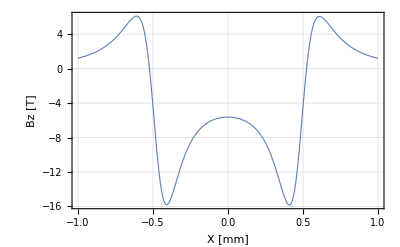

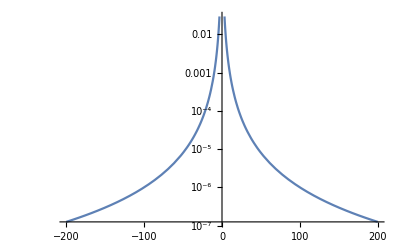

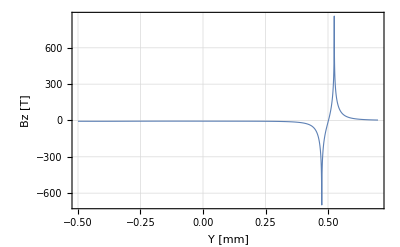

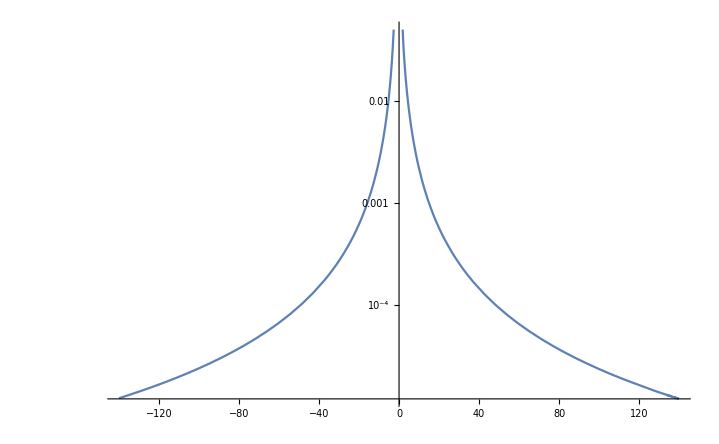

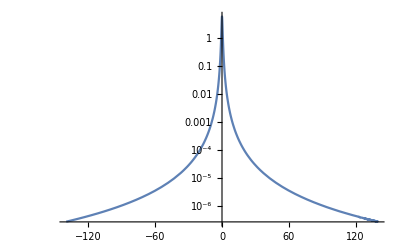

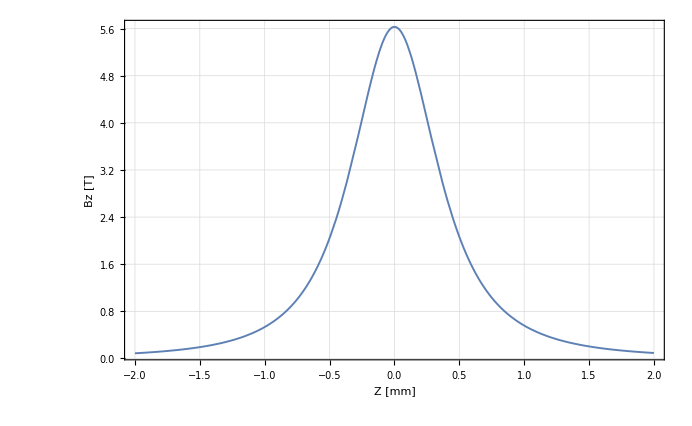

Get::noopen: 无法打开 Graphics`PlotField`.

Table::nliter: 位置 2 处的非列表迭代器(non-list iterator) PlotRange→{{-1,1},{-1,1},{-1,1}} 没有算出实数值.

Table[VectorPlot3D[{Bx[xx,yy,zz],By[xx,yy,zz],Bz[xx,yy,zz]},{xx,0,1},{yy,0,0.5},{zz,0,2}],PlotRange→{{-1,1},{-1,1},{-1,1}},VectorScale→{0.1,1,None},VectorPoints→{6,6,5},VectorStyle→{Arrow3D,Red},RegionFunction→Function[{x,y,z},x^2+y^2+2 z^2<1^2],Boxed→True,Axes→False]

-Graphics-

```mathematica
RadPlot3DOptions[];
dr=radObjDrw[Grp];
Show[Graphics3D[dr,Axes->True,AxesStyle->{Red,Green,Blue},LabelStyle->Directive[Bold,20],TicksStyle-> Directive[20],Boxed->True,ImageSize->1000]]

RadPlotOptions[];
Plot[radFld[Grp,"Bz",{x,0,0}],{x,-1.0,1.0}
,AxesOrigin->{0,0}
,FrameLabel->{"X [mm]","Bz [T]","Y = Z =  0",""}]
RadPlotOptions[];
LogPlot[Abs[radFld[Grp,"Bz",{x,0,0}]],{x,-200,200}
,AxesOrigin->{0,0}
,FrameLabel->{"X [mm]","Bz [T]","Y = Z =  0",""}]

RadPlotOptions[];
Plot[radFld[Grp,"Bz",{0,y,0}],{y,-0.5,0.7}
,AxesOrigin->{0,0}
,FrameLabel->{"Y [mm]","Bz [T]","X = Z =  0",""}]
RadPlotOptions[];
LogPlot[Abs[radFld[Grp,"Bz",{0,y,0}]],{y,-140,140}
,AxesOrigin->{0,0}
,FrameLabel->{"Y [mm]","Bz [T]","X = Z =  0",""}]

RadPlotOptions[];
LogPlot[Abs[radFld[Grp,"Bz",{0,0,z}]],{z,-140,140}
,AxesOrigin->{0,0}
,FrameLabel->{"Z [mm]","Bz [T]","X = Y = 0",""}]
RadPlotOptions[];
Plot[Abs[radFld[Grp,"Bz",{0,0,z}]],{z,-2,2}
,AxesOrigin->{0,0}
,FrameLabel->{"Z [mm]","Bz [T]","X = Y = 0",""}]
(*<<VectorFieldPlots`;
Needs["VectorFieldPlots`"]
*)

(*Table[VectorPlot3D[{Bx[xx,yy,zz],By[xx,yy,zz],Bz[xx,yy,zz]},{xx,0,1},{yy,0,0.5},{zz,0,2}]]*)
(*ListVectorFieldPlot3D[Flatten[Table[{{0,0,0},{Bx,By,Bz}},{x,0,1,0.2},{y,0,1,0.2},{z,0,1,0.2}],2]]
*)

(*ListPlotVectorField3D[radObjM["B",{x,y,z}],
VectorHeads -> True,
ColorFunction -> Hue,
PlotRange ->{{-1,1},{-1,1},{-1,1}},
ScaleFactor->0]

*)

<<Graphics`PlotField`;


Table[VectorPlot3D[{Bx[xx,yy,zz],By[xx,yy,zz],Bz[xx,yy,zz]},{xx,0,1},{yy,0,0.5},{zz,0,2}],
PlotRange->{{-1,1},{-1,1},{-1,1}},VectorScale->{0.1,1,None},VectorPoints->{6,6,5},VectorStyle->{"Arrow3D",Red},RegionFunction->Function[{x,y,z},x^2+y^2+2 z^2<1^2],Boxed->True,Axes->False]
```